# Genetic Algorithms Code - Growth Data

## General Settings

### Setting the Directory

```mathematica
SetDirectory[NotebookDirectory[]];
(* Some unimportant error messages are switched off for future convenience *)
Off[ListInterpolation::inhr];
ParallelEvaluate@Off[General::munfl];
```

### Various Constants

```mathematica
(* Planck18 Values and other constants *)
obh2pl = 0.02237;
obh2plerr = 0.00015;
ompl = 0.3153;
omplerr = 0.0073;
σ8pl = 0.8111;
σ8err = 0.0060;
h0pl = 0.6736;
h0riess = 73.04/100;
Tcmb=2.7255;
c = 299792.458;
cH0=2997.92458;
```

## Genetic Algorithms Theory

### Genetic Algorithms Basics

```mathematica
poly[x_]:=x
polyxtox[x_]:=x^x
(* grammar={poly,Exp,Sin,Cos,Tan,Log};*)
grammar={poly,polyxtox};
(* Expression length *)
length=4;
depth=4;
rang1={-1,1};
rang2={1,Length[grammar]};
rang3={-9,9};
rang4={0,9};
toursize=4;
selectionrate=0.3;
```

```mathematica
func[x_,kid_,gram_]:=Sum[kid[[i,1]] (gram[[kid[[i,2]]]]@(kid[[i,3]] x))^kid[[i,4]],{i,1,length}]
mutation[kid_]:=Module[{mut,rep},
rep={RandomInteger[{1,length}],RandomInteger[{1,depth}]};
mut=Which[rep[[2]]==1,RandomReal[rang1],rep[[2]]==2,RandomInteger[rang2],rep[[2]]==3,RandomReal[rang3],rep[[2]]==4,RandomReal[rang4]];
ReplacePart[kid,rep->mut]]
cross[{kid1_,kid2_}]:=Module[{len},len=RandomInteger[{1,length-1}];
{Join[kid1[[1;;len]],kid2[[(len+1);;-1]]],Join[kid1[[(len+1);;-1]],kid2[[1;;len]]]}]
```

```mathematica
tournament[fit_,tours_]:=Sort[RandomSample[fit,tours],#1[[1]]>#2[[1]]&][[1,2]]
negativetournament[fit_,tours_]:=Sort[RandomSample[fit,tours],#1[[1]]>#2[[1]]&][[-1,2]]
```

```mathematica
GAevo[randomseed_,maxgens_,pop_,crossrate_,mutrate_,verbose_]:=Module[{prog,bestfitperstep,chromosomes,t1,pigs,fitness,p1,p2,maxchilds},
maxchilds=Round[selectionrate*pop,2];
SeedRandom[randomseed];
ParallelEvaluate[SeedRandom[randomseed]];
bestfitperstep={};
chromosomes=ParallelTable[{RandomReal[rang1],RandomInteger[rang2],RandomReal[rang3],RandomInteger[rang4]},{pop},{length}];
t1=AbsoluteTime[];
Do[pigs=(x-x^4 func[x,#,grammar]^2)&/@chromosomes;
fitness=Sort[ParallelTable[{-MemoryConstrained[TimeConstrained[chi2[pigs[[j]]],.5],10^7],j},{j,1,Length[pigs]}],#1[[1]]>#2[[1]]&];AppendTo[bestfitperstep,{fitness[[1,1]],pigs[[fitness[[1,2]]]],chromosomes[[fitness[[1,2]]]]}];p1=Partition[RandomSample[Table[negativetournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];p2=Partition[RandomSample[Table[tournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];Do[{chromosomes[[p1[[jj,1]]]],chromosomes[[p1[[jj,2]]]]}=If[RandomReal[{0,1}]<crossrate,
cross[{chromosomes[[p2[[jj,1]]]], chromosomes[[p2[[jj,2]]]]}],{chromosomes[[p1[[jj,1]]]],chromosomes[[p1[[jj,2]]]]}];,{jj,1,Length[p1]}];Do[{chromosomes[[p1[[jj,1]]]],chromosomes[[p1[[jj,2]]]]}=If[RandomReal[{0,1}]<mutrate,
{mutation[chromosomes[[p2[[jj,1]]]]],mutation[chromosomes[[p2[[jj,2]]]]]},{chromosomes[[p1[[jj,1]]]],chromosomes[[p1[[jj,2]]]]}];,{jj,1,Length[p1]}];
prog`int++,{maxgens}];
If[verbose==True,
Print["Time taken: ",AbsoluteTime[]-t1," sec"];
Print["χ_min^2 = ",Abs[fitness[[1,1]]]];
Print["Best-fit function is: "];
Print[bestfitperstep[[-1,2]]];
Speak["The end"];];
bestfitperstep]
```

## Real Data Analysis - ΛCDM Model

### Basic Functions for the wCDM Model

```mathematica
(* Note that in the dynamical data case we use directly the analytical expressions for the wCDM instead of the nCPL model that we did in the background data. This choice does not affect the overall results, since we only use them for the ΛCDM case. *)
Hwcdm[a_,w_,om_]:=√(om a^-3+(1-om)a^(-3(1+w)));
(* Growth for wCDM models *)
δ[a_,w_,Ω_]:=a Hypergeometric2F1[1/(-3w),1/2-1/(2 w),1-5/(6 w),a^(-3 w) (1-1/Ω)]
fwCDM[a_,w_,Ω_]:=aa D[Log[δ[aa,w,Ω]],aa]/.aa->a
fσ8wCDM[a_,w_,Ω_,σ8_]:=fwCDM[a,w,Ω]σ8  δ[a,w,Ω]/δ[1,w,Ω]
dAh[a_,om_,w_]:=(2a)/(√om)(Hypergeometric2F1[1/2,-1/(6w),1-1/(6w),1-1/om]-√a Hypergeometric2F1[1/2,-1/(6w),1-1/(6w),(1-1/om)a^(-3w)]);
```

### Growth data

#### Import the Growth Compilation

```mathematica
datagrowth=Import["./data/growth_data_2022.txt","Table"][[2;;-1]]/.{z_,f_,s_,om_}->{1/(1+z),f,s,om};
ndatgrowth=Length[datagrowth]
```

20

#### χ^2 of Growth

```mathematica
(* Add support for WiggleZ and eBOSS data Cij *)
Cijwigglez=Import["./data/Cij_WiggleZ.txt","Table"];
CijeBOSS=Import["./data/sdss_DR12_LRG_FSBAO_DMDHfs8_covtot.txt","Table"][[{3,6},{3,6}]];
```

```mathematica
(* Support term for WiggleZ and SDSS Cij *)
Wigglez={4,5,6};
eBOSS={16,17};
Cijfs8=DiagonalMatrix[datagrowth[[All,3]]^2];
Cijfs8[[Wigglez,Wigglez]]=Cijwigglez;
Cijfs8[[eBOSS,eBOSS]]=CijeBOSS;
InvCijfs8=Inverse[Cijfs8];
(* Fiducial Subscript[Ω, m] from paper *)
omf=datagrowth[[All,4]];
```

```mathematica
(* Corrections due to the fiducial cosmology *)
ratiogrowth[a_,om_,w_,omfid_]:=((Hwcdm[a,w,om]dAh[a,om,w])/(Hwcdm[a,-1,omfid] dAh[a,omfid,-1]));
(* χ^2 correlated term *)
vecgrowth[om_,w_,σ8_]:=Table[datagrowth[[i,2]]-fσ8wCDM[datagrowth[[i,1]],w,om,σ8]/ratiogrowth[datagrowth[[i,1]],om,w,omf[[i]]],{i,1,ndatgrowth}]
chi2growth[om_,w_,σ8_]:=vecgrowth[om,w,σ8].InvCijfs8.vecgrowth[om,w,σ8]
```

#### Growth Data - Maximum Likelihood Method for ΛCDM

```mathematica
mingrowth=FindMinimum[chi2growth[om,-1,σ8],{om,0.3,0.31},{σ8,0.8,0.81}];
ombfgrowth=mingrowth[[2,1,2]];
σ8bfgrowth=mingrowth[[2,2,2]];
chifungrowth=ListInterpolation[ParallelTable[chi2growth[om,-1,σ8],{om,ombfgrowth-0.02,ombfgrowth+0.02,0.02},{σ8,σ8bfgrowth-0.02,σ8bfgrowth+0.02,0.02},DistributedContexts->Automatic],{{ombfgrowth-0.02,ombfgrowth+0.02},{σ8bfgrowth-0.02,σ8bfgrowth+0.02}}];
(* Params that we want to calculate the errors *)
paramsgrowth={om,σ8};
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
Fijgrowth=1/2 Table[D[chifungrowth[om,σ8],paramsgrowth[[p]],paramsgrowth[[d]]]/.mingrowth[[2]],{p,1,Length[paramsgrowth]},{d,1,Length[paramsgrowth]}];
cijgrowth=Inverse[Fijgrowth];
errorsgrowth=Sqrt[Diagonal[cijgrowth]];
Print["The best fit parameter for Ω_(0  m) and σ_8 is: Ω_(0  m)=",ombfgrowth,"±",errorsgrowth[[1]]," and σ_8=",σ8bfgrowth,"±",errorsgrowth[[2]]," with a χ^2 value: χ^2=",mingrowth[[1]]]
```

The best fit parameter for Ω_(0  m) and σ_8 is: Ω_(0  m)=0.260162±0.0339953 and σ_8=0.823308±0.0355267 with a χ^2 value: χ^2=16.0608

## Genetic Algorithms

### Genetic Algorithms Theory

#### Specific χ^2 Functions - GA

```mathematica
H0GA=67.17004414248437;
hGA=H0GA/100;
HGA[a_]:=H0GA√(1+x (-0.8999883844902956+0.2620381909322407 (1+0.15327819800211584 x)^3-0.381979946511561 (1+1.6189955164319452 x))^2)/.x->1/a-1
dAGA[a_]:=cH0/hGA x (1+(0.8718351321839224-0.12885030729521135 x)^2 x)/(1+x)^2/.x->1/a-1
```

```mathematica
(* Corrections due to the fiducial cosmology *)
ratioGA[a_,omfid_]:=((HGA[a]dAGA[a])/(100cH0 Hwcdm[a,-1,omfid] dAh[a,omfid,-1]));
(* χ^2 for GA *)
chi2GAmarg[fs8GA_]:=Module[{A,B,Γ,yi,ythi},
yi=datagrowth[[All,2]];
ythi=Table[(fs8GA/.x->datagrowth[[i,1]])/ratioGA[datagrowth[[i,1]],omf[[i]]],{i,1,Length[datagrowth]}];
A=yi.InvCijfs8.yi;
B=yi.InvCijfs8.ythi+ythi.InvCijfs8.yi;
Γ=ythi.InvCijfs8.ythi;
A-B^2/(4Γ)]
chi2[fs8GA_]:=Module[{temp},
temp=chi2GAmarg[fs8GA];If[MatchQ[temp,_Real]&&$MinNumber<temp<$MaxNumber,temp,1. 10^230]]
```

### Genetic Algorithms Calculations

#### Main Loop

```mathematica
t1=AbsoluteTime[];
generations=1500;
samples=10;
prog`int=0;prog`pop=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
ProgressIndicator[Dynamic[prog`pop],{0,samples}]
(* {randomseed, maxgens, population, crossoverrate, mutationrate, verbose (True/False)} *)
Do[GApop[jj]=GAevo[123jj,generations,100,0.75,0.25,False];prog`pop++;prog`int=0;,{jj,1,samples}];
Print["Time Taken: ",(AbsoluteTime[]-t1)/60," minutes"]
```

$Aborted

Time Taken: 0.0340716 minutes

#### Derived Results

```mathematica
(* The results are presented in the form {Subscript[d, L](x), H(x), # of sample} *)
fGAdistro=Table[{GApop[jj][[-1,2]],GApop[jj][[-1,1]],jj},{jj,1,samples}]
chi2tab=Table[{GApop[jj][[-1,1]]//Abs,jj},{jj,1,samples}]
Select[chi2tab,#[[1]]<mingrowth[[1]]&]
```

{{x-x^4 (0.911716-0.136826 x^3.09842)^2,-17.9871,1},{x-x^4 (0.868506-0.477412 x^3+0.315405 (0.787768^(0.787768 x) x^(0.787768 x))^3.99852+0.305508 (0.788323^(0.788323 x) x^(0.788323 x))^1.14432)^2,-16.582,2},{x-x^4 (1.01542-0.40319 x^2.57933+0.542168 (0.614488^(0.614488 x) x^(0.614488 x))^3.74732)^2,-16.4777,3},{x-x^4 (1.00997-0.240618 x^3.33621+0.0521822 (0.701076^(0.701076 x) x^(0.701076 x))^6.67788)^2,-17.0612,4},{x-(-0.919482+0.148237 x^0.988654)^2 x^4,-18.9138,5},{x-x^4 (1.17538-0.708978 (0.766655^(0.766655 x) x^(0.766655 x))^5.52301-0.701977 (0.766655^(0.766655 x) x^(0.766655 x))^6.96523)^2,-17.6028,6},{x-x^4 (-0.153871 x^2.7279+0.661222 (0.13573^(0.13573 x) x^(0.13573 x))^0.218336+0.330611 (0.13573^(0.13573 x) x^(0.13573 x))^0.249985)^2,-17.7289,7},{x-x^4 (-0.336591+2.41497 (0.293997^(0.293997 x) x^(0.293997 x))^2.10853)^2,-18.5768,8},{x-x^4 (1.107-0.322752 x^1.6897)^2,-17.0272,9},{x-x^4 (-0.411552 x^1.53327+0.00288789 x^5.68044+1.68016 (0.0725866^(0.0725866 x) x^(0.0725866 x))^1.71982)^2,-15.6929,10}}

{{17.9871,1},{16.582,2},{16.4777,3},{17.0612,4},{18.9138,5},{17.6028,6},{17.7289,7},{18.5768,8},{17.0272,9},{15.6929,10}}

{{15.6929,10}}

```mathematica
Rasterize[ListLogLogPlot[Table[GApop[jj][[All,1]]//Abs,{jj,1,samples}],Joined->True,PlotRange->{10,700},Frame->True,FrameStyle->Black,Epilog->{Dashed,Line[{{0.1,mingrowth[[1]]},{generations,mingrowth[[1]]}}//Log]},FrameLabel->{"N","χ^2(N)"},FrameStyle->Black,BaseStyle->FontSize->14,PlotLegends->Automatic],ImageSize->700]
```

-Graphics-

```mathematica
fGAdistro[[10]]
chi2tab[[10]]
```

{x-x^4 (-0.411552 x^1.53327+0.00288789 x^5.68044+1.68016 (0.0725866^(0.0725866 x) x^(0.0725866 x))^1.71982)^2,-15.6929,10}

{15.6929,10}

#### 1σ Errors

```mathematica
fs8GA0[x_]:=x-x^4 (-0.4115523329512044 x^1.5332714921897406+0.002887890644749495 x^5.680438572566711+1.6801627335784026 (0.07258660144352902^(0.07258660144352902 x) x^(0.07258660144352902 x))^1.7198211539830677)^2
(* χ^2 correlated term *)
vecGA[fs8GA_]:=Table[datagrowth[[i,2]]-(fs8GA/.x->datagrowth[[i,1]])/ratioGA[datagrowth[[i,1]],omf[[i]]],{i,1,Length[datagrowth]}]
chi2GA[fs8GA_]:=vecGA[fs8GA].InvCijfs8.vecGA[fs8GA]
FindMinimum[chi2GA[fs8c fs8GA0[x]],{fs8c,1.1,1.11}]
```

{15.6929,{fs8c→1.10938}}

```mathematica
fs8c0=1.10938192906447;
fs8GA[x_]:=fs8c0 fs8GA0[x]
δfs8[x_,a1_,a2_,a3_]:=x(a1+a2 x+a3 x^2)
```

```mathematica
Dij=CholeskyDecomposition[(InvCijfs8+Transpose[InvCijfs8])/2];
yj=datagrowth[[All,2]];

fbfj=Table[fs8GA[datagrowth⟦j,1⟧]/ratioGA[datagrowth⟦j,1⟧,omf⟦j⟧],{j,1,Length[datagrowth]}];
```

```mathematica
chi2confGA[a1_?NumericQ,a2_?NumericQ,a3_?NumericQ]:=Module[{δfj,vec1,vec2,conf},
δfj=Table[δfs8[datagrowth⟦j,1⟧,a1,a2,a3]/ratioGA[datagrowth⟦j,1⟧,omf⟦j⟧],{j,1,Length[datagrowth]}];
vec1=-Dij.(+yj-fbfj+δfj);
vec2=-Dij.(-yj+fbfj+δfj);
conf=Table[1/2 (Erf[vec1[[i]]/(√2) ]+Erf[vec2[[i]]/(√2) ])/Erf[1/(√2)],{i,1,Length[datagrowth]}];
Sum[(conf[[k]]-1)^2,{k,1,Length[datagrowth]}]]
```

```mathematica
chi2tot[a1_?NumericQ,a2_?NumericQ,a3_?NumericQ]:=chi2confGA[a1,a2,a3]+chi2[fs8GA[x]+δfs8[x,a1,a2,a3]]
```

```mathematica
fminfs8err=FindMinimum[chi2tot[a1,a2,0],{a1,0.01,0.011},{a2,0.011,0.0111}]
```

{17.5475,{a1→-0.353505,a2→0.256503}}

### Comparison with ΛCDM

#### fσ_8(z) Plot

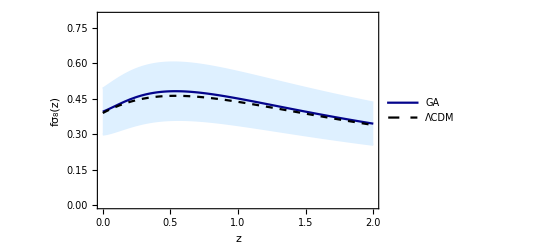

```mathematica
ϵ0={-1,0,1};
col=GrayLevel[0.3,0.2];
plt=Plot[{fs8GA[1/(1+z)]+δfs8[1/(1+z),a1,a2,0]ϵ0/.fminfs8err[[2]]//Evaluate,fσ8wCDM[1/(1+z),-1,ombfgrowth,σ8bfgrowth]},{z,0,2},PlotStyle->{LightBlue,RGBColor["#04048c"],LightBlue,{Black,Dashed}},Filling->{1->{{3},LightBlue}},Frame->True,ImageSize->400,FrameLabel->{"z","fσ_8(z)"},PlotRange->{All,{0,0.8}},FrameStyle->Black,BaseStyle->FontSize->16,PlotLegends->Placed[LineLegend[{RGBColor["#04048c"],Dashed},{"GA","ΛCDM"}],Scaled[{0.8,0.8}]],Axes->None]
```

```mathematica
Export[NotebookDirectory[]<>"fs8plot.pdf",plt,ImageResolution->600];
```